# Metoda celor mai mici patrate

```mathematica
x={1,2,3,4,5,6,7};
y={1.2,1.9,2.8,4.1,5.2, 5.9,7.1};
n=Dimensions[x][[1]]
```

7

```mathematica
xm=(∑_(i=1)^n x[[i]])/n;ym=(∑_(i=1)^n y[[i]])/n;
xym=(∑_(i=1)^n x[[i]]*y[[i]])/n;x2m=(∑_(i=1)^n x[[i]]*x[[i]])/n;
y2m=(∑_(i=1)^n y[[i]]*y[[i]])/n;
sxx2=∑_(i=1)^n (x[[i]]-xm)^2;sxy2=∑_(i=1)^n (x[[i]]-xm)*(y[[i]]-ym);syy2=∑_(i=1)^n (y[[i]]-ym)^2;
r2=sxy2^2/(sxx2*syy2);
```

```mathematica
a=(ym*x2m-xm*xym)/(x2m-xm^2)
b=(xym-ym*xm)/(x2m-xm^2)
r2
```

0.0142857

1.00357

0.994571

```mathematica
Y[X]=a+b*X;
```

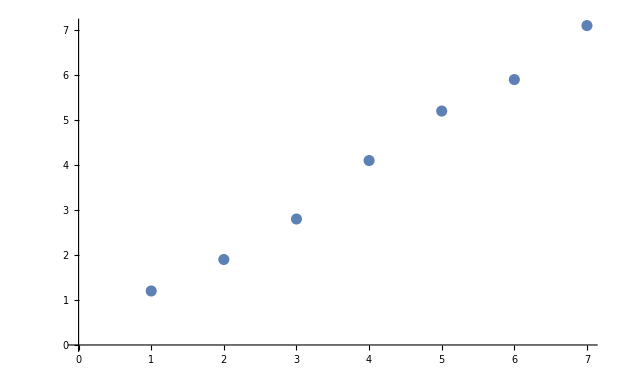

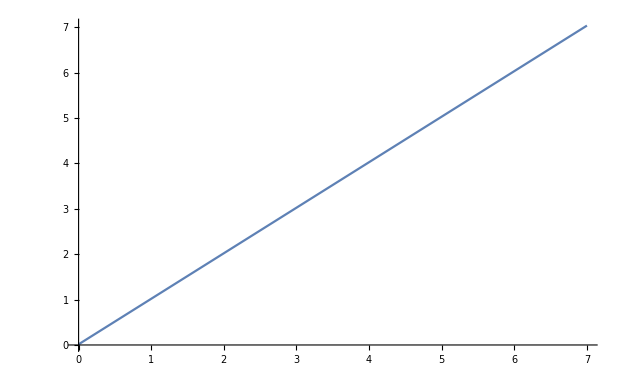

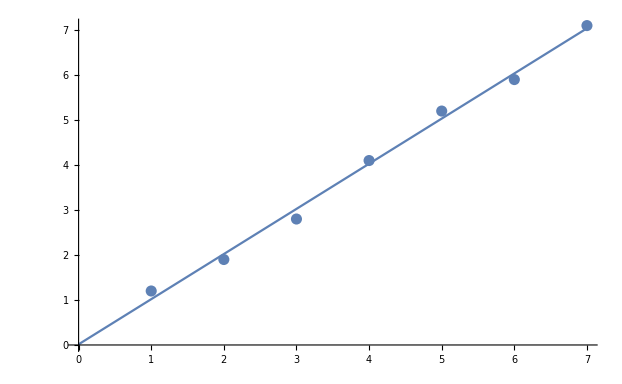

```mathematica
p1=ListPlot[Table[{x[[i]],y[[i]]},{i,1,n}]]
p2=Plot[a+b*X,{X,0,x[[n]]}]
Show[p1,p2]
```